# SciML: Day 1

## Created by: Juan Osorio

## Poisson equation 1D

The analytical solution of the proposed PDE in the Jupyter notebook poisson.ipynb looks like this

```mathematica
Clear[u,x]
(*Solve analitically the PDE, actually an ODE for this 1D case*)
FullSimplify[DSolve[{-u''[x] == Sin[x],u[0]==0,u[1]==0}, u[x], x]]
```

{{u[x]→-x Sin[1]+Sin[x]}}

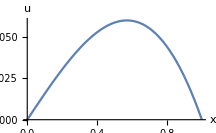

```mathematica
(*Define the solution*)
u[x_]:=-x*Sin[1]+Sin[x]
(*Plot the solution*)
Plot[u[x],{x,0,1},AxesLabel->{x,u}]
```

## Laplace equation 2D

```mathematica
(* Specify the PDE *)
pde = ∇_{x,y}^2 u[x,y] == 0; 
(* Specify the Boundary Conditions *)
bc = DirichletCondition[u[x,y] == Sin[x*y], True];
(*Solve it !*)
NDSolveValue[{pde, bc}, u, {x,y} ∈ Disk[]]
```

InterpolatingFunction[…]

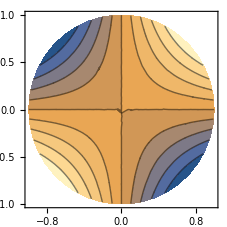

```mathematica
ContourPlot[%[x, y], {x, y} ∈ Disk[]]
```